```mathematica
Clear[G11,G22,G12,Nulls,P,G]
```

```mathematica
G11[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo-zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G22[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p ((-J+Jtwo+zR)-Jone Cos[k]-(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
G12[J_,Jone_,Jtwo_,p_,zR_Real]:=NIntegrate[(p (Jtwo+Jone Cos[k]+(2 Jtwo) Cos[k]^2))/((2 π) ((J^2-2 J Jtwo-zR^2)+(2 J Jone) Cos[k]+(4 J Jtwo) Cos[k]^2)),{k,-π,π}]
```

```mathematica
Nulls[Jtwo_,z_]:=1-G11[1,0.1,Jtwo,-0.3,z]-G22[1,0.1,Jtwo,-0.3,z]-G12[1,0.1,Jtwo,-0.3,z]^2+G11[1,0.1,Jtwo,-0.3,z]G22[1,0.1,Jtwo,-0.3,z]
FindRoot[Nulls[-0.005,z]==0,{z,0.6804106657898775}]
```

{z→0.679729}

```mathematica
√(J^4/(J^2+J u)+(J^3 u)/(J^2+J u)+(J^2 u^2)/(2 (J^2+J u))+(J u^3)/(8 (J^2+J u))-1/(8 (J^2+J u))(√(256 J^4 J q^2+512 J^3 J q^2 u+64 J^6 u^2+320 J^2 J q^2 u^2+96 J^5 u^3+64 J  J q^2 u^3+52 J^4 u^4+12 J^3 u^5+J^2 u^6)))/.{J->1,q->0.1,u->2*-0.3}
```

0.680411

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[Nulls[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[Nulls[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.6804106657898775]]
```

{{0.005,0.680947},{0.01,0.681338},{0.015,0.681587},{0.02,0.681693},{0.025,0.681659},{0.03,0.681485},{0.035,0.681174},{0.04,0.680727},{0.045,0.680144},{0.05,0.679428},{0.055,0.678579},{0.06,0.677599},{0.065,0.676489},{0.07,0.675251},{0.075,0.673886},{0.08,0.672395},{0.085,0.670779},{0.09,0.669039},{0.095,0.667177},{0.1,0.665193}}

```mathematica
moduler[Lister[-1,-0.005,0.6804106657898775]]
```

{{-0.005,0.679729},{-0.01,0.6789},{-0.015,0.677922},{-0.02,0.676795},{-0.025,0.675517},{-0.03,0.674087},{-0.035,0.672504},{-0.04,0.670767},{-0.045,0.668875},{-0.05,0.666827},{-0.055,0.664623},{-0.06,0.66226},{-0.065,0.659739},{-0.07,0.657059},{-0.075,0.65422},{-0.08,0.651219},{-0.085,0.648058},{-0.09,0.644735},{-0.095,0.64125},{-0.1,0.637602}}

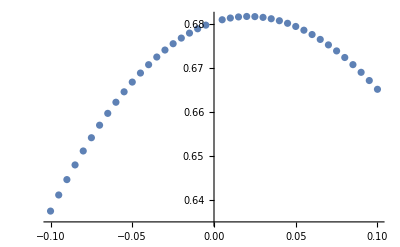

```mathematica
P = ListPlot[{{0.005,0.6809467728901929},{0.01,0.6813383043059662},{0.015,0.6815865865319956},{0.02,0.6816929638764102},{0.025,0.6816587939350585},{0.03,0.6814854430595491},{0.035,0.6811742818511155},{0.04,0.6807266807075637},{0.045,0.6801440054462794},{0.05,0.6794276130219881},{0.055,0.6785788473529457},{0.06,0.6775990352669781},{0.065,0.6764894825742798},{0.07,0.675251470271149},{0.075,0.673886250885426},{0.08,0.6723950448960629},{0.085,0.6707790374214491},{0.09,0.6690393748446057},{0.095,0.6671771616862979},{0.1,0.6651934575357478},{-0.005,0.6797286788057545},{-0.01,0.6788995344307871},{-0.015,0.6779219861144029},{-0.02,0.6767948223433731},{-0.025,0.6755168704778548},{-0.03,0.6740870002926711},{-0.035,0.6725041271473988},{-0.04,0.6707672147259671},{-0.045,0.6688752772735292},{-0.05,0.6668273812603259},{-0.055,0.664622646401626},{-0.06,0.6622602459637014},{-0.065,0.6597394062878302},{-0.07,0.6570594054675116},{-0.075,0.6542195711186718},{-0.08,0.6512192771858955},{-0.085,0.6480579397386724},{-0.09,0.6447350117147279},{-0.095,0.6412499765688157},{-0.1,0.6376023408081004}}]
```

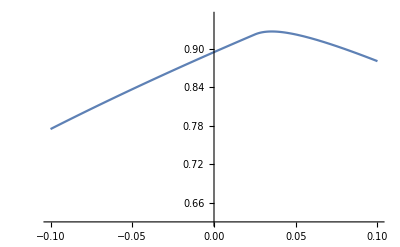

```mathematica
G = Plot[Sqrt[1+2*(0.1*Cos[Inv[0.1,Jtwo]]+Jtwo*Cos[2*Inv[0.1,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.63,0.95}]
```

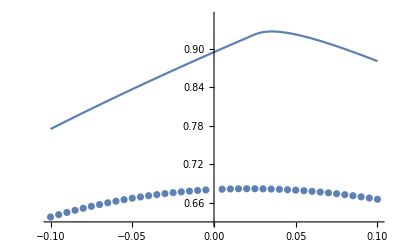

```mathematica
Show[G,P]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.1,moduler[Lister[-1,-0.005,0.6804106657898775]]]
```

{{-0.005,0.209091},{-0.01,0.204277},{-0.015,0.199574},{-0.02,0.194985},{-0.025,0.190509},{-0.03,0.186146},{-0.035,0.181896},{-0.04,0.177761},{-0.045,0.17374},{-0.05,0.169833},{-0.055,0.16604},{-0.06,0.162361},{-0.065,0.158796},{-0.07,0.155344},{-0.075,0.152006},{-0.08,0.148781},{-0.085,0.145667},{-0.09,0.142666},{-0.095,0.139775},{-0.1,0.136994}}

```mathematica
differ[1,0.1,moduler[Lister[1,0.005,0.6804106657898775]]]
```

{{0.005,0.219053},{0.01,0.2242},{0.015,0.229457},{0.02,0.234822},{0.025,0.436375},{0.03,0.244077},{0.035,0.245417},{0.04,0.245286},{0.045,0.244218},{0.05,0.242527},{0.055,0.240413},{0.06,0.238006},{0.065,0.235398},{0.07,0.23265},{0.075,0.22981},{0.08,0.22691},{0.085,0.223977},{0.09,0.221029},{0.095,0.218082},{0.1,0.215147}}

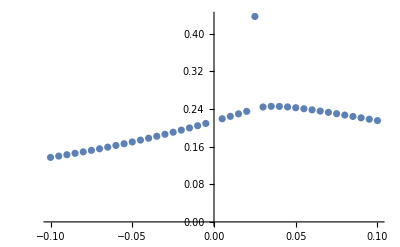

```mathematica
ListPlot[{{-0.005,0.20909076292580442},{-0.01,0.20427655220199759},{-0.015,0.19957445262480933},{-0.02,0.1949849663647616},{-0.025,0.1905085333065838},{-0.03,0.18614552641159154},{-0.035,0.18189624738435428},{-0.04,0.1777609226978899},{-0.045,0.17373970004410655},{-0.05,0.16983264527374964},{-0.055,0.1660397398901814},{-0.06,0.16236087915983066},{-0.065,0.15879587089941472},{-0.07,0.1553444349960844},{-0.075,0.15200620371118323},{-0.08,0.1487807228141046},{-0.085,0.14566745358070476},{-0.09,0.14266577568645322},{-0.095,0.13977499102184976},{-0.1,0.136994328433383},{0.005,0.21905322710980712},{0.01,0.22420020950777542},{0.015,0.22945677138243437},{0.02,0.23482217511475778},{0.025,0.43637519481483644},{0.03,0.24407744873477233},{0.035,0.24541701347354306},{0.04,0.245286278165043},{0.045,0.24421763614452374},{0.05,0.2425268327073007},{0.055,0.24041269479826177},{0.06,0.23800641105438003},{0.065,0.23539782490316374},{0.07,0.23265034946803098},{0.075,0.22980986322963792},{0.08,0.22691024253418446},{0.085,0.22397692667944347},{0.09,0.22102928667664012},{0.095,0.21808224127213194},{0.1,0.2151473855472027}}]
```